```mathematica
Integrate[(x-Sqrt[ArcTan[2x]])/(1+4x^2),x]
```

-1/3 ArcTan[2 x]^(3/2)+1/8 Log[1+4 x^2]

```mathematica
Integrate[(x-Sqrt[ArcTan[2x]])/(1+4x^2),{x,0,1}]
```

-1/3 ArcTan[2]^(3/2)+Log[5]/8

```mathematica
N[%]
```

-0.187138

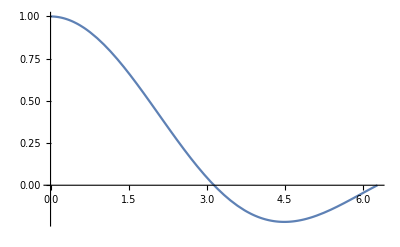

```mathematica
Plot[(Sin[x])/x,{x,0,2Pi}]
```

```mathematica
FindRoot[(Sin[x])/x,{x,3}]
```

{x→3.14159}

```mathematica
Abs[Integrate[(Sin[x])/x,{x,0,Pi}]]+Abs[Integrate[(Sin[x])/x,{x,Pi,2Pi}]]
```

2 SinIntegral[π]-SinIntegral[2 π]

```mathematica
N[%]
```

2.28572

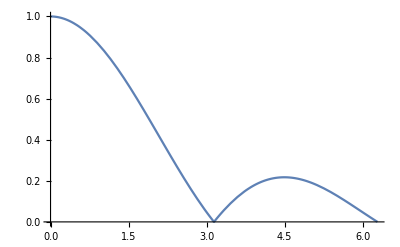

```mathematica
Plot[Abs[(Sin[x])/x],{x,0,2Pi}]
```

```mathematica
NIntegrate[Abs[(Sin[x])/x],{x,0,2Pi}]
```

2.28572

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=2x+1
```

1+2 x

```mathematica
Plot[{f[x],g[x]}{x,2,3}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

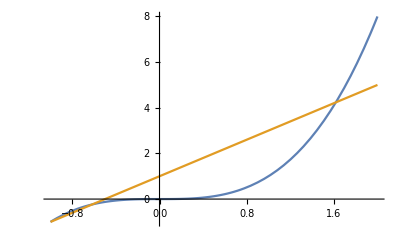

```mathematica
Plot[{f[x],g[x]} ,{x,-1,2}]
```

```mathematica
Solve[f[x]==g[x],x]
```

{{x→-1},{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
Abs[Integrate[f[x]-g[x],{x,-1,1/2 (1-√5)}]]+Abs[Integrate[f[x]-g[x],{x,1/2 (1-√5),1/2 (1+√5)}]]
```

```mathematica
-11/8+(15 √5)/8
```

```mathematica
Integrate[Abs[f[x]-g[x]],{x,-1,1/2 (1+√5)}]
```

1/8 (-11+15 √5)

NIntegrate::inumr: The integrand cos[x]/(1+x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand cos[x]/(1 + x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

```mathematica
Trapezis[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+2*Sum[f[a+k*h],{k,1,n-1}]+f[b])*h/2,20]]
```

```mathematica
A[x_]= Cos[x]/(1+x)
```

Cos[x]/(1+x)

```mathematica
NIntegrate[A[x],{x,0,1}]
```

0.601044

```mathematica
Trapezis[A, {0,1,10}]
```

0.60141412919716912939

```mathematica
Abs[A''[x]]
```

Abs[(2 Cos[x])/(1+x)^3-Cos[x]/(1+x)+(2 Sin[x])/(1+x)^2]

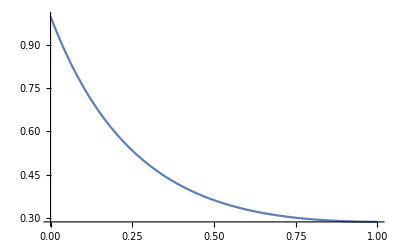

```mathematica
Plot [Abs[A''[x]],{x,0,1}]
```

```mathematica
N[1/1200]
```

0.000833333

```mathematica
Simpson[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+4*Sum[f[a+(2*k+1)*h],{k,0,n/2-1}]+2*Sum[f[a+2*k*h],{k,1,n/2-1}]+f[b])*h/3,20] ]
```

```mathematica
A''''[x]
```

(24 Cos[x])/(1+x)^5-(12 Cos[x])/(1+x)^3+Cos[x]/(1+x)+(24 Sin[x])/(1+x)^4-(4 Sin[x])/(1+x)^2

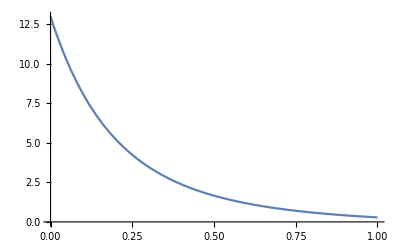

```mathematica
Plot[(24 Cos[x])/(1+x)^5-(12 Cos[x])/(1+x)^3+Cos[x]/(1+x)+(24 Sin[x])/(1+x)^4-(4 Sin[x])/(1+x)^2,{x,0,1}]
```

```mathematica
Abs[A''''[0]]
```

13

```mathematica
Reduce[13/(180*n^4)<10^-11,n]
```

n<-(100 √5 26^(1/4))/(√3)||n>(100 √5 26^(1/4))/(√3)

```mathematica
N[%]
```

n<-291.52||n>291.52

```mathematica
Simpson[A,{0,1,292}]
```

0.6010443852566021759